```mathematica
(* https://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/heart-model.html*)
isoContractPhase={(-x1[t]+Subscript[R, R] x4[t])/(Subscript[C, R](Subscript[R, 2]+Subscript[R, R])),0,(-x3[t]-Subscript[R, L] x4[t])/(Subscript[C, L](Subscript[R, 1]+Subscript[R, L])),
(-x4[t])/L(Subscript[R, B]+(Subscript[R, 1] Subscript[R, L])/(Subscript[R, 1]+Subscript[R, L])+(Subscript[R, 2] Subscript[R, R])/(Subscript[R, 2]+Subscript[R, R]))+(Subscript[R, L] x3[t])/(L(Subscript[R, 1]+Subscript[R, L]))-(Subscript[R, R] x1[t])/(L(Subscript[R, 2]+Subscript[R, R]))};
ejectionPhase={(-x1[t]+Subscript[R, R] x4[t])/(Subscript[C, R](Subscript[R, 2]+Subscript[R, R])),
(-(Subscript[R, 1]+Subscript[R, L])Subscript[E, v] x2[t]-Subscript[R, L] x3[t]-Subscript[R, 1] Subscript[R, L] x4[t])/Subscript[R, T],
(Subscript[R, L] Subscript[E, v] x2[t]-(Subscript[R, L]+Subscript[R, A])x3[t]-Subscript[R, L] Subscript[R, A] x4[t])/(Subscript[C, L] Subscript[R, T]),
(-Subscript[R, R]x1[t])/(L(Subscript[R, 2]+Subscript[R, R]))+(Subscript[R, 1] Subscript[R, L] Subscript[E, v] x2[t]+Subscript[R, L] Subscript[R, A] x3[t]-(Subscript[R, 1] Subscript[R, L] Subscript[R, A]+Subscript[R, G] Subscript[R, T])x4[t])/(Subscript[R, T] L)};
isoRelaxPhase=isoContractPhase;
fillingPhase={(-x1[t]+Subscript[R, R] x4[t])/(Subscript[C, R](Subscript[R, 2]+Subscript[R, R])),(-Subscript[E, v]x2[t])/Subscript[R, M]+Subscript[P, AS]/Subscript[R, M],
(-x3[t]-Subscript[R, L] x4[t])/(Subscript[C, L](Subscript[R, 1]+Subscript[R, L])),(-x4[t])/L(Subscript[R, B]+(Subscript[R, 1] Subscript[R, L])/(Subscript[R, 1]+Subscript[R, L])+(Subscript[R, 2] Subscript[R, R])/(Subscript[R, 2]+Subscript[R, R]))+(Subscript[R, L] x3[t])/(L(Subscript[R, 1]+Subscript[R, L]))-(Subscript[R, R] x1[t])/(L(Subscript[R, 2]+Subscript[R, R]))};
```

```mathematica
Subscript[a, 1][v_]:=Piecewise[{{2.1*^-3 v^2 10^6-10^3 0.2338v+10.6,v≤0.055},
		{-1.0133*^-3 v^2 10^6-10^3 0.0626v+10.6,True}}];
Subscript[a, 2][v_]:=
Piecewise[{{150.0/1000,v≤0.055},{-6*v+0.48,True}}];
Subscript[a, 3][v_]:=
	Piecewise[{{2.8*^-3 v^2 10^6-10^3 0.3v+10.2,v≤0.055},
{6.476*^-4 v^2 10^6-10^3 0.1816v+10.2,True}}];
Subscript[b, 1][v_]:=-1.*^-4v 10^3+0.0157;
Subscript[b, 2][v_]:=45.0/1000;
Subscript[b, 3][v_]:=-4.*^-4v 10^3+0.0431;
Subscript[c, 1][v_]:=9.7*^-6 v^2 10^6-10^3 2.8*^-4v+0.12;
Subscript[c, 2][v_]:=0.06;
Subscript[c, 3][v_]:=-40.2*^-6 v^2 10^6+10^3 4.78*^-3v+0.06;
d=100.0;
f[v_,t_]:=1000Sum[Subscript[a, i][v]Exp[-(1000 Subscript[b, i][v](t-Subscript[c, i][v]))^2]+d,{i,1,3}];
activeElas=f[Subscript[V, ed],t-tstartelastance[t]]-f[Subscript[V, ed],0]+10^3 (10.6 Subscript[V, ed]^2-0.147 Subscript[V, ed]+0.00234)/Subscript[V, ed];
passiveElas=10^3 (10.6x2[t]^2-0.147x2[t]+0.00234)/x2[t];
```

```mathematica
xinit={29, 0.0352,30, 0.0047};
initconds={{x1[0],x2[0],x3[0],x4[0]}==xinit, phase[0]==1, tstartelastance[0]==0};
heartParameters={Subscript[R, A]->60,Subscript[R, M]->22};
arterialParameters={Subscript[C, L]->2.35*^-4,Subscript[R, 1]->60,Subscript[C, R]->1.33*^-4,Subscript[R, 2]->300,Subscript[R, L]->12640,Subscript[R, B]->60,Subscript[R, R]->8550,L->21.9};
derivedParameters={Subscript[R, T]->Subscript[R, 1] Subscript[R, A]+Subscript[R, 1] Subscript[R, L]+Subscript[R, A] Subscript[R, L],Subscript[R, G]->Subscript[R, B](1+Subscript[R, 2]/(Subscript[R, 2]+Subscript[R, R]))};
pressureParameters={Subscript[P, v]->x2[t] Subscript[E, v],Subscript[P, A]->x3[t]+x3'[t] Subscript[C, L] Subscript[R, 1],Subscript[P, AS]->10};
params=Join[heartParameters,arterialParameters,derivedParameters,pressureParameters,{Subscript[V, ed]->xinit[[2]]}];
```

```mathematica
isoContParams=Join[params,{Subscript[E, v]->activeElas}];
ejectionParams=Join[params,{Subscript[E, v]->activeElas}];
isoRelaxParams=Join[params,{Subscript[E, v]->activeElas}];
fillingParams=Join[params,{Subscript[E, v]->passiveElas}];
```

```mathematica
isoContractPhase=isoContractPhase//.isoContParams;
ejectionPhase=ejectionPhase//.ejectionParams;
isoRelaxPhase=isoRelaxPhase//.isoRelaxParams;
fillingPhase=fillingPhase//.fillingParams;
```

```mathematica
vars={x1[t],x2[t],x3[t],x4[t]};
state={isoContractPhase,ejectionPhase,isoRelaxPhase,fillingPhase};
eqns={
x1'[t]==Piecewise[Table[{state[[i,1]],phase[t]==i},{i,1,4}]],
x2'[t]==Piecewise[Table[{state[[i,2]],phase[t]==i},{i,1,4}]],
x3'[t]==Piecewise[Table[{state[[i,3]],phase[t]==i},{i,1,4}]],
x4'[t]==Piecewise[Table[{state[[i,4]],phase[t]==i},{i,1,4}]]
};
```

```mathematica
ev1=WhenEvent[And[!(Subscript[P, AS]<Subscript[P, v]<Subscript[P, A]),phase[t]==1],
	{phase[t]->2,Sow[t,1]}]//.isoContParams;
ev2=WhenEvent[And[!(Subscript[P, A]<Subscript[P, v]),phase[t]==2],
	{phase[t]->3,Sow[t,2]}]//.ejectionParams;
ev3=WhenEvent[And[!(Subscript[P, AS]<1.001 Subscript[P, v]<Subscript[P, A]),phase[t]==3],
	{phase[t]->4,Sow[t,3]}]//.isoRelaxParams;
ev4=WhenEvent[And[!(1.001 Subscript[P, v]<Subscript[P, AS]),phase[t]==4],
	{phase[t]->1,tstartelastance[t]->t,Sow[t,4]}]//.fillingParams;
```

```mathematica
events={ev1,ev2,ev3,ev4};
```

```mathematica
{sol,times}=NDSolveValue[{eqns,initconds,events},vars,{t,0,4},DiscreteVariables->{Element[phase,{1,2,3,4}],tstartelastance[t]}]//Reap;
```

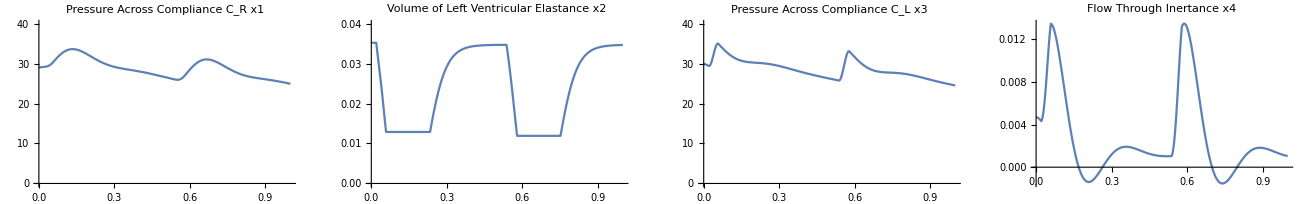

```mathematica
GraphicsGrid[{{Plot[sol[[1]],{t,0,1},PlotRange->{0,40},PlotLabel->"Pressure Across Compliance C_R x1"],
Plot[sol[[2]],{t,0,1},PlotRange->{0,0.04},PlotLabel->"Volume of Left Ventricular Elastance x2"],
Plot[sol[[3]],{t,0,1},PlotRange->{0,40},PlotLabel->"Pressure Across Compliance C_L x3"],
Plot[sol[[4]],{t,0,1},PlotRange->All,PlotLabel->"Flow Through Inertance x4"]}}]
```